```mathematica
netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[Tanh],3,ElementwiseLayer[Sin]},2],{}],"Input"->"Real"];
NetGraphPlot[netInit,ImageSize->Small]
```

-Graphics-

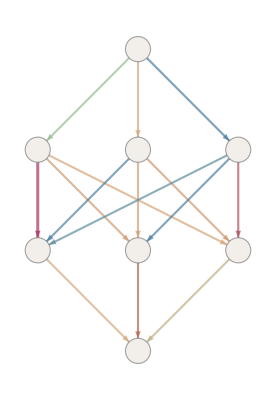
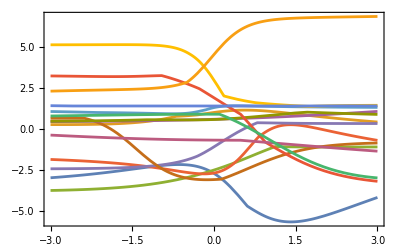
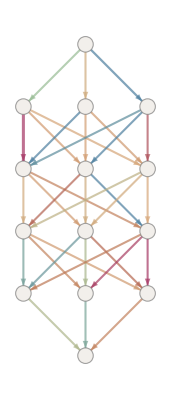
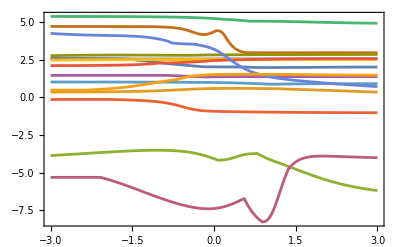
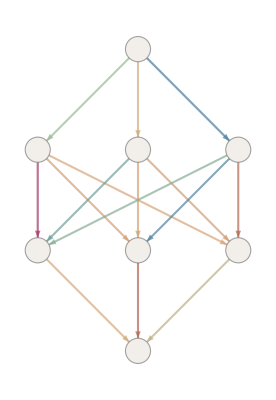
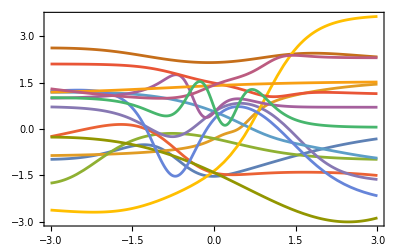
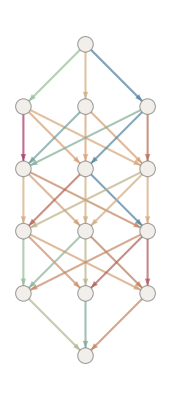
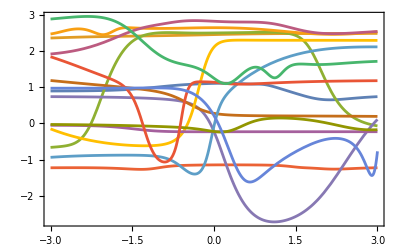
{Tanh and Ramp,-Graphics-
-Graphics-,-Graphics-
-Graphics-} | {Tanh and Sin,-Graphics-
-Graphics-,-Graphics-
-Graphics-}
{LogisticSigmoid and Ramp,-Graphics-
-Graphics-,-Graphics-
-Graphics-} | {LogisticSigmoid and Sin,-Graphics-
-Graphics-,-Graphics-
-Graphics-}

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth},netPlots=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]]/@(NetChain[Append[Catenate@Table[{3,ElementwiseLayer[#2],3,ElementwiseLayer[#3]},#],{}],"Input"->"Real"]&@@@Tuples[{depths,activationsLayer1,activationsLayer2}]);
SeedRandom[1234];
plots=Table[Prepend[Text[ToString[act1]<>" and "<>ToString[act2]]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"]},Column[{Rotate[ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInit,ImageSize->Tiny],90 Degree],Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]}]],{depth,depths}],{act1,activationsLayer1},{act2,activationsLayer2}];
Grid[plots]]
normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

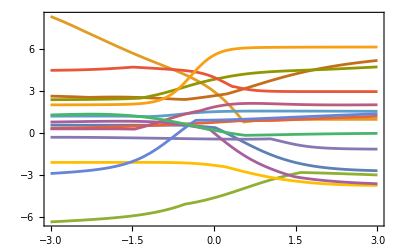
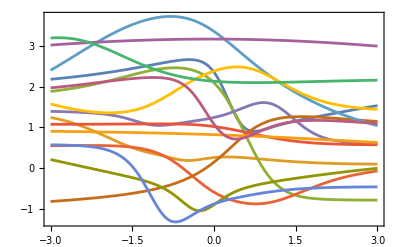
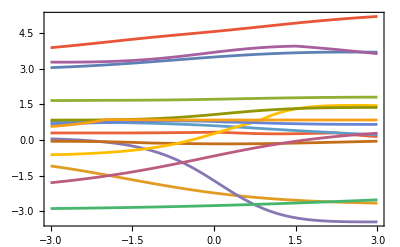
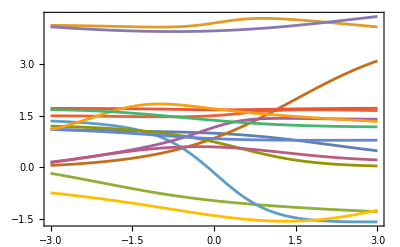
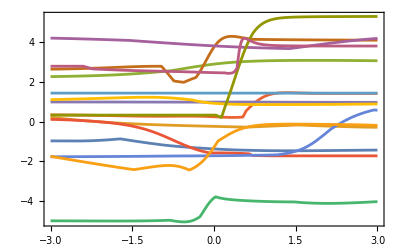
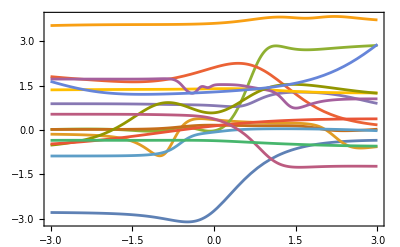
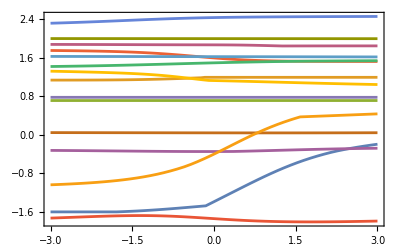
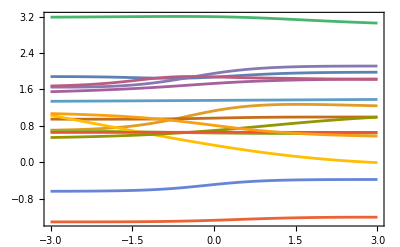
| {Tanh and Ramp,Tanh and Sin} | {LogisticSigmoid and Ramp,LogisticSigmoid and Sin}
{Tanh and Ramp,Tanh and Sin} | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
{LogisticSigmoid and Ramp,LogisticSigmoid and Sin} | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
 | -Graphics- | -Graphics-

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}];
architecturePlots=Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
activationLabels=Prepend[activationLabels,""];
outputPlots=MapThread[Prepend,{outputPlots,activationLabels[[2;;]]}];
Grid[Prepend[Append[outputPlots,Prepend[architecturePlots,""]],activationLabels]]]

normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

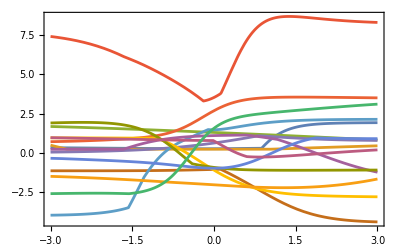
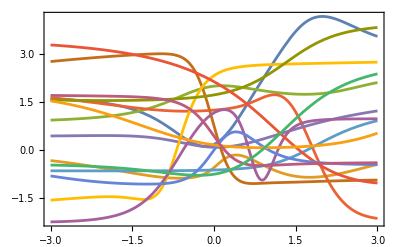
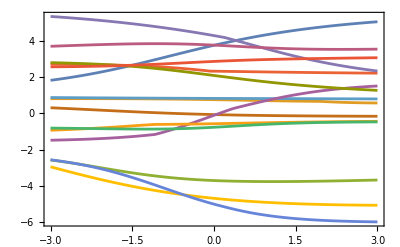
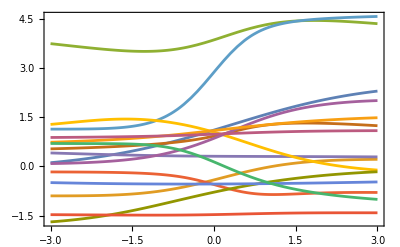
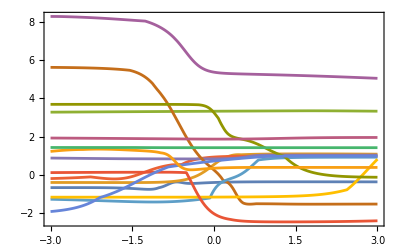
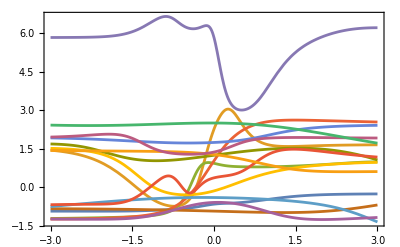
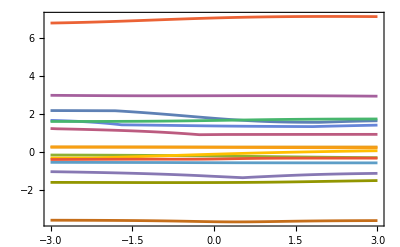
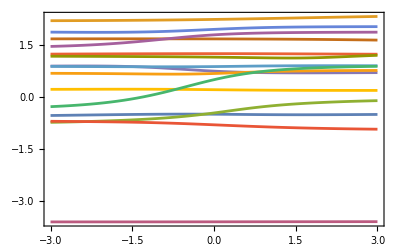
| Tanh and Ramp | Tanh and Sin | LogisticSigmoid and Ramp
{,Tanh and Ramp} | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-} | 
{Tanh and Sin,LogisticSigmoid and Ramp} | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-} | 
 | -Graphics- | -Graphics- |

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
activationLabels=Prepend[activationLabels,""];
outputPlots=MapThread[Prepend,{outputPlots,Partition[activationLabels,Length[activationsLayer2]]}];
Grid[Prepend[Append[outputPlots,Prepend[architecturePlots,""]],activationLabels[[;;Length[activationLabels]-1]]],Dividers->All]]

normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

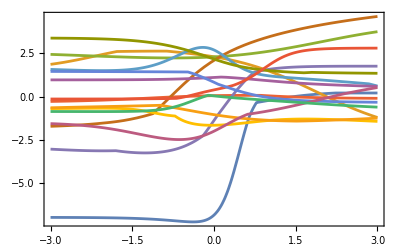
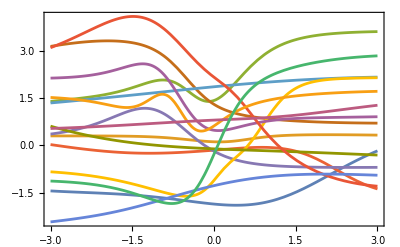
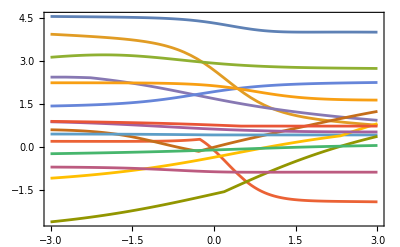
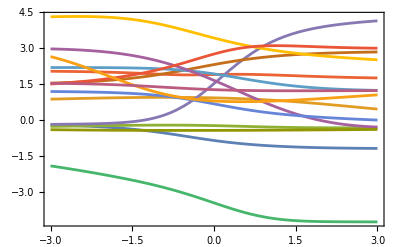
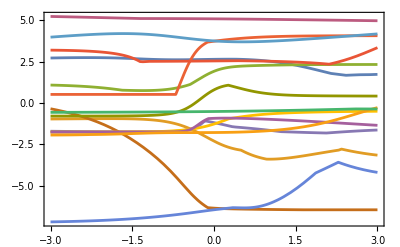
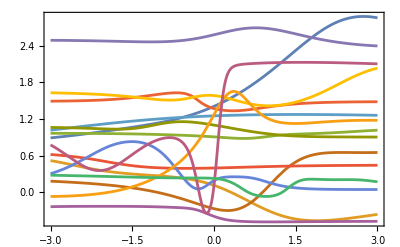
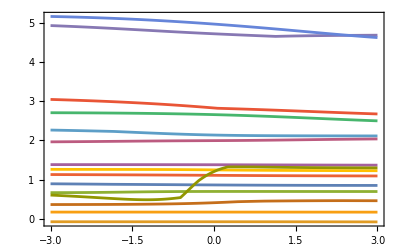
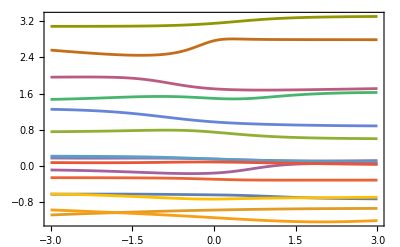
|  | 
Tanh and Ramp | -Graphics- | -Graphics-
Tanh and Sin | -Graphics- | -Graphics-
LogisticSigmoid and Ramp | -Graphics- | -Graphics-
LogisticSigmoid and Sin | -Graphics- | -Graphics-
 | -Graphics- | -Graphics-

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Table[Rotate[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],Pi/2],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
labeledOutputPlots=MapThread[Prepend,{Partition[Flatten[outputPlots],Length[depths]],activationLabels}];
Grid[Join[Prepend[labeledOutputPlots,Prepend[ConstantArray["",Length[depths]],""]],{Prepend[architecturePlots,""]}],Dividers->All]]
normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

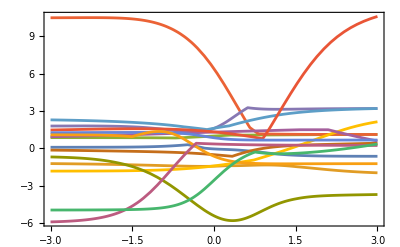
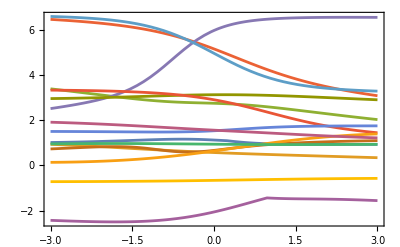
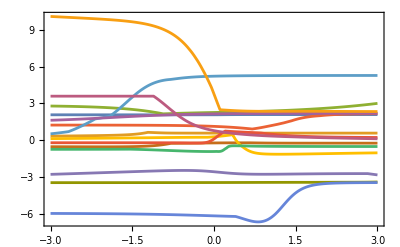
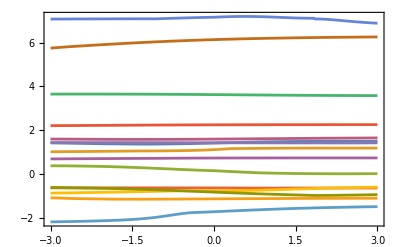
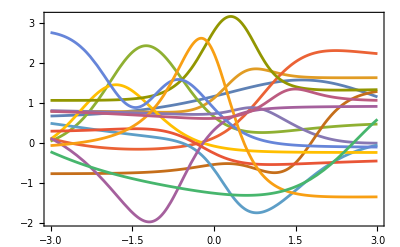
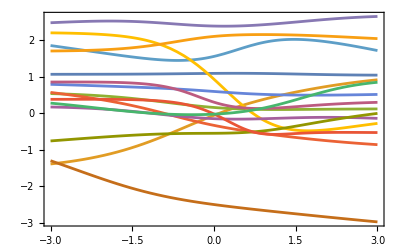
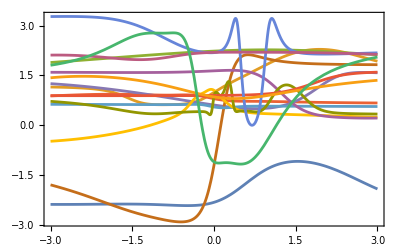
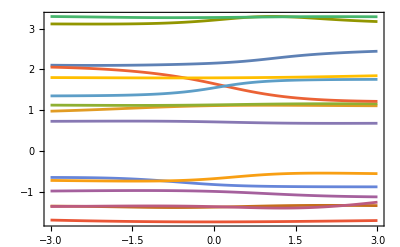
|  |  |  | 
 | Tanh and Ramp | Tanh and Sin | LogisticSigmoid and Ramp | LogisticSigmoid and Sin
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Rotate[#,Pi/2]&/@Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
labeledOutputPlots=Partition[Flatten[Table[Prepend[Table[outputPlots[[d,i,j]],{j,Length[activationsLayer2]}],architecturePlots[[d]]],{d,Length[depths]},{i,Length[activationsLayer1]}]],Length[activationsLayer2]+1];
Grid[Prepend[Join[{Prepend[activationLabels,""]},Transpose[labeledOutputPlots]],Prepend[ConstantArray["",Length[activationLabels]],""]],Dividers->All]]
normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

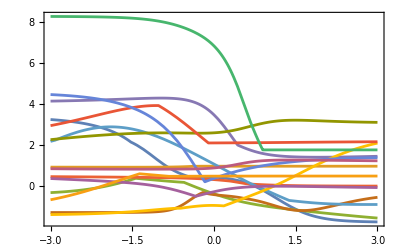
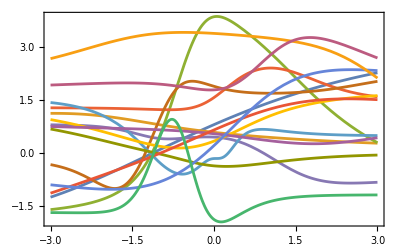
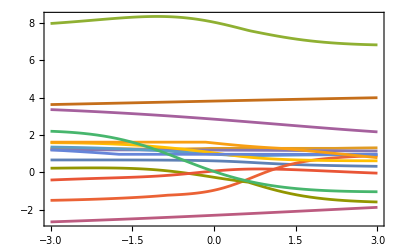
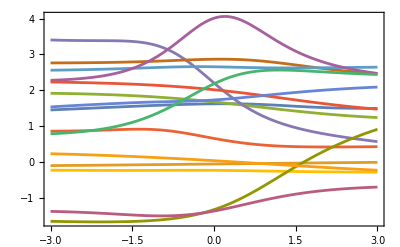
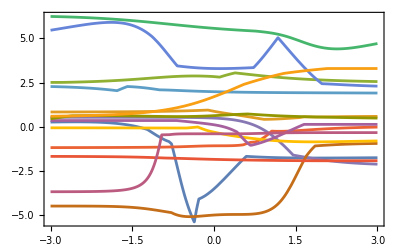
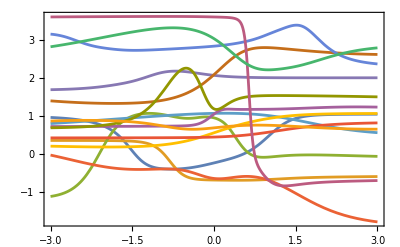
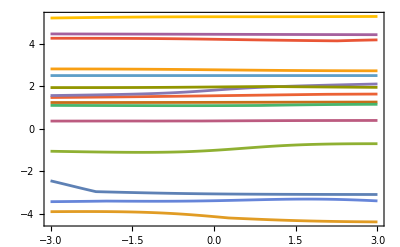
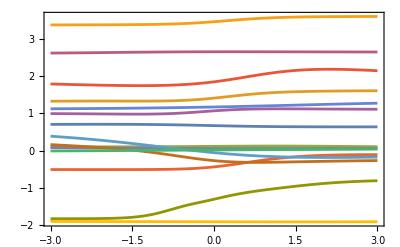
|  |  |  | 
 | Tanh and Ramp | Tanh and Sin | LogisticSigmoid and Ramp | LogisticSigmoid and Sin
{} | {} |  |  | 
-Graphics- | -Graphics- |  |  | 
{-Graphics-,{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} | {-Graphics-,{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} |  |  |

```mathematica
normalMultiLayerNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Rotate[#,Pi/2]&/@Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
labeledOutputPlots=Table[Prepend[outputPlots[[d,All,All]],architecturePlots[[d]]],{d,Length[depths]}];
Grid[Prepend[Join[{Prepend[activationLabels,""]},Transpose[Join[{{""},##}&@@@Transpose[{architecturePlots,labeledOutputPlots}]]]],Prepend[ConstantArray["",Length[activationLabels]],""]],Dividers->All]]

normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2},1]
```

```mathematica
gammaTwoFunctionNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,alpha_,beta_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Rotate[#,Pi/2]&/@Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
labeledOutputPlots=MapThread[Prepend,{Partition[Flatten[outputPlots],Length[depths]],activationLabels}];
Grid[Join[Prepend[labeledOutputPlots,Prepend[ConstantArray["",Length[depths]],""]],{Prepend[architecturePlots,""]}],Dividers->All]]
```

```mathematica
gammaTwoFunctionNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2,3,4},1,1 ]
```

$Aborted

```mathematica
uniformTwoFunctionNetworkPlot[activationsLayer1_,activationsLayer2_,depths_,min_,max_]:=Module[{netPlots,netInit,f,plots,act1,act2,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots},netInitChain[act1_,act2_,depth_]:=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act1],3,ElementwiseLayer[act2]},depth],{}],"Input"->"Real"];
netPlots[act1_,act2_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[act1,act2,depth]];
activationLabels=Flatten[Table[Text[ToString[act1]<>" and "<>ToString[act2]],{act1,activationsLayer1},{act2,activationsLayer2}]];
architecturePlots=Rotate[#,Pi/2]&/@Table[netPlots[activationsLayer1[[1]],activationsLayer2[[1]],depth],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[act1,act2,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->UniformDistribution[{min,max}],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{act1,activationsLayer1},{act2,activationsLayer2}];
labeledOutputPlots=MapThread[Prepend,{Partition[Flatten[outputPlots],Length[depths]],activationLabels}];
Grid[Join[Prepend[labeledOutputPlots,Prepend[ConstantArray["",Length[depths]],""]],{Prepend[architecturePlots,""]}],Dividers->All]]
```

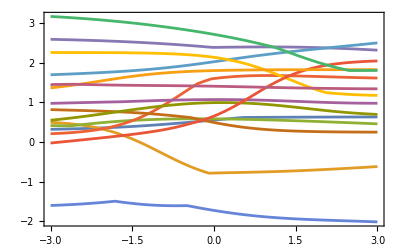
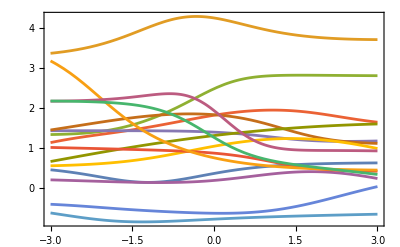
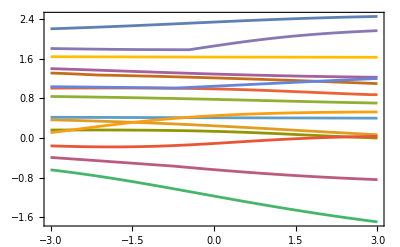
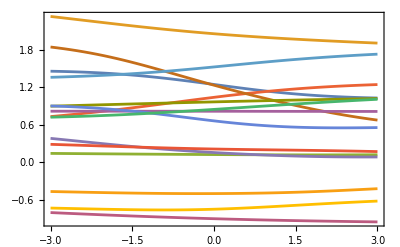
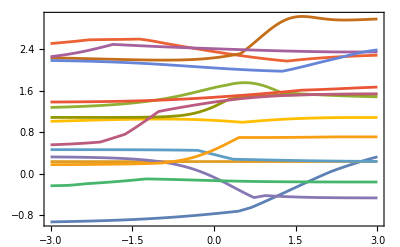
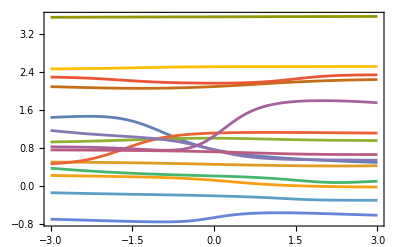
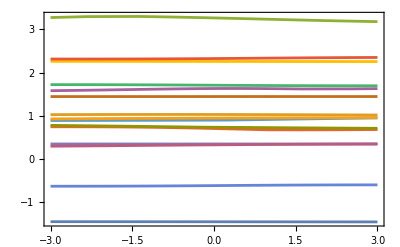
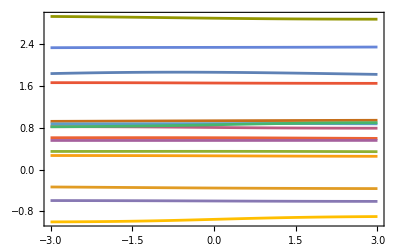
|  |  | 
Tanh and Ramp | -Graphics- | -Graphics- | -Graphics-
Tanh and Sin | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid and Ramp | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid and Sin | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics-

```mathematica
uniformTwoFunctionNetworkPlot[{Tanh,LogisticSigmoid},{Ramp,Sin},{1,2,3},-1,1]
```

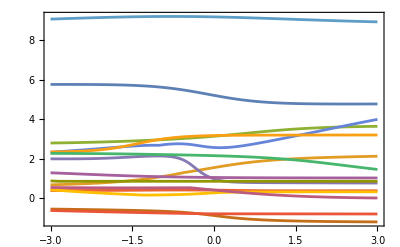
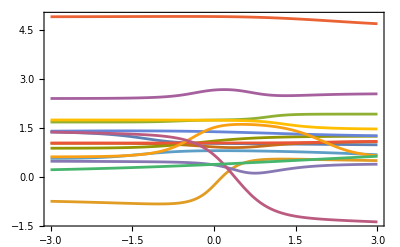
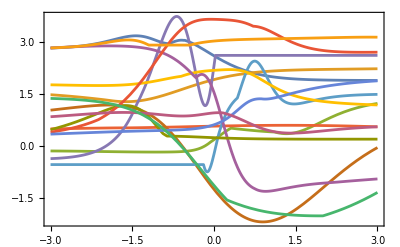
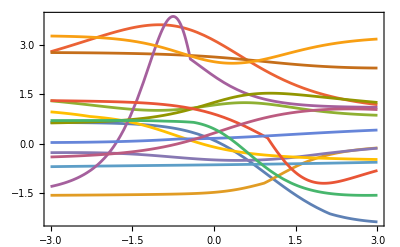
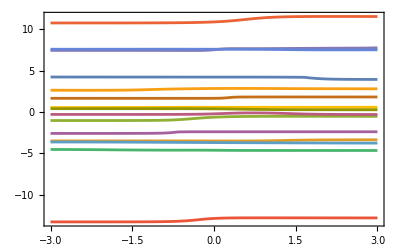
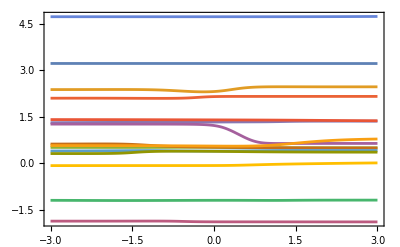
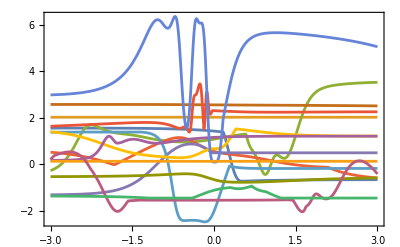
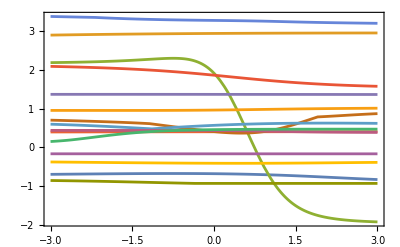
|  | 
Tanh and LogisticSigmoid and Ramp | -Graphics- | -Graphics-
Tanh and LogisticSigmoid and Sin | -Graphics- | -Graphics-
Tanh and Ramp and Sin | -Graphics- | -Graphics-
LogisticSigmoid and Ramp and Sin | -Graphics- | -Graphics-
 | -Graphics- | -Graphics-

```mathematica
normalMultiLayerNetworkPlot[activationsList_,depths_,sigma_]:=Module[{netPlots,netInit,f,plots,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots,layerActivations},netInitChain[activations_,depth_]:=NetChain[Append[Flatten[Table[{3,ElementwiseLayer[act]},{act,activations},depth],1],1],"Input"->"Real"];
netPlots[activations_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[activations,depth]];
activationLabels=Table[Text[StringJoin@Riffle[ToString/@activations," and "]],{activations,Subsets[activationsList,{3}]}];
architecturePlots=Table[Rotate[netPlots[Take[activationsList,3],depth],Pi/2],{depth,depths}];
SeedRandom[1234];outputPlots=Table[With[{netInit=netInitChain[activations,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[0,sigma],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{activations,Subsets[activationsList,{3}]}];
labeledOutputPlots=MapThread[Prepend,{Partition[Flatten[outputPlots],Length[depths]],activationLabels}];
Grid[Join[Prepend[labeledOutputPlots,Prepend[ConstantArray["",Length[depths]],""]],{Prepend[architecturePlots,""]}],Dividers->All]]
normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid,Ramp,Sin},{1,2},1]
```

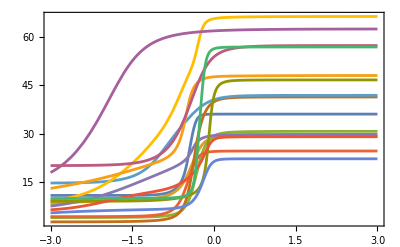
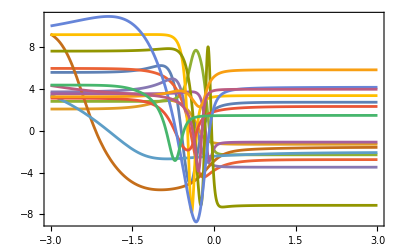
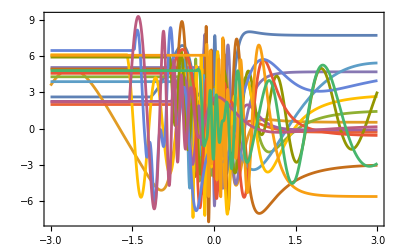
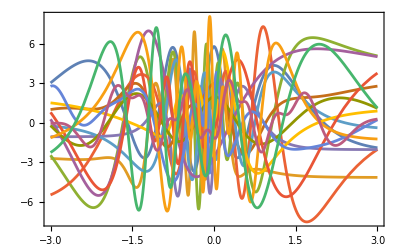
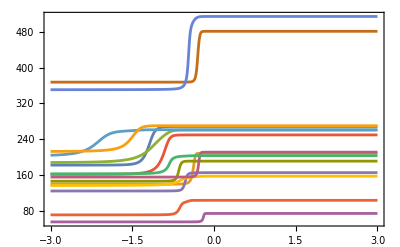
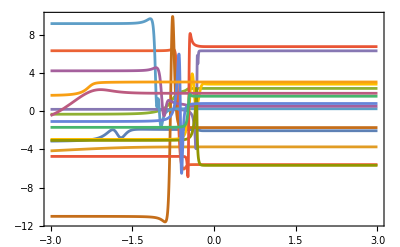
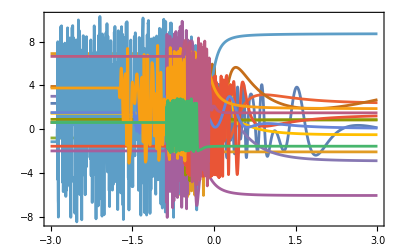
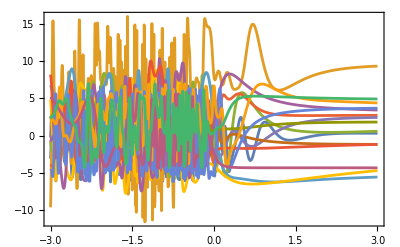
|  | 
Tanh and LogisticSigmoid and Ramp | -Graphics- | -Graphics-
Tanh and LogisticSigmoid and Sin | -Graphics- | -Graphics-
Tanh and Ramp and Sin | -Graphics- | -Graphics-
LogisticSigmoid and Ramp and Sin | -Graphics- | -Graphics-
 | -Graphics- | -Graphics-

```mathematica
normalMultiLayerNetworkPlot[activationsList_,depths_,alpha_,beta_]:=Module[{netPlots,netInit,f,plots,depth,activationLabels,architecturePlots,outputPlots,netInitChain,labeledOutputPlots,layerActivations},netInitChain[activations_,depth_]:=NetChain[Append[Flatten[Table[{3,ElementwiseLayer[act]},{act,activations},depth],1],1],"Input"->"Real"];
netPlots[activations_,depth_]:=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][netInitChain[activations,depth]];
activationLabels=Table[Text[StringJoin@Riffle[ToString/@activations," and "]],{activations,Subsets[activationsList,{3}]}];
architecturePlots=Table[Rotate[netPlots[Take[activationsList,3],depth],Pi/2],{depth,depths}];
SeedRandom[1234];
outputPlots=Table[With[{netInit=netInitChain[activations,depth]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[alpha,beta],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,depths},{activations,Subsets[activationsList,{3}]}];
labeledOutputPlots=MapThread[Prepend,{Partition[Flatten[outputPlots],Length[depths]],activationLabels}];
Grid[Join[Prepend[labeledOutputPlots,Prepend[ConstantArray["",Length[depths]],""]],{Prepend[architecturePlots,""]}],Dividers->All]]
normalMultiLayerNetworkPlot[{Tanh,LogisticSigmoid,Ramp,Sin},{1,2},2,1]
```